0.924207

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

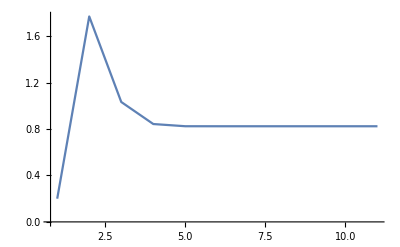

```mathematica
f[x_]:=x^2-Cos[x];
NewtonRhapsonStep[x_]:=x-f[x]/f'[x];
NewtonRhapsonStep[0.5]
NewtonRhapson[x0_,n_]:=Block[{soluciones = {x0},x = x0},
Do[
x = NewtonRhapsonStep[x];
AppendTo[soluciones,x]; (* Añado el nuevo x a la lista *)
,
n (* Número de repeticiones *)
];

soluciones
];
listaDeSoluciones = NewtonRhapson[0.2,10]
ListLinePlot[listaDeSoluciones,PlotRange->All]
```

```mathematica
Error[x_]:=-f''[x]/(2f'[x]);
Error[0.2]
```

```mathematica
Map[Error,{listaDeSoluciones}]
```

{{-2.48891,-0.19929,-0.429357,-0.547553,-0.562172,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331}}

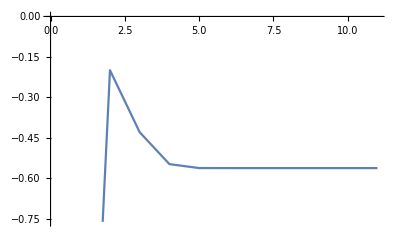

```mathematica
ListLinePlot[Map[Error,{listaDeSoluciones}]]
```